## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

```mathematica
cb2 ⅇ^(-ⅈ ϕ)
```

cb2 ⅇ^(-ⅈ ϕ)

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb2,cd1}=B[𝓇,𝓉].{cb3,cd2};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
```

### Result (BS1,3 are 50-50 beam splitters and we post select on modes a and b having vacuum)

```mathematica
cof=CoefficientList[Expand[out[ca2,cb3,2]],{ca2,cb3}];
cof2=CoefficientList[Collect[Simplify[cof[[1,1]]],{cc3,cd3}],{cc3,cd3}];
Simplify[cof2[[1,1]]]
{Simplify[cof2[[2,1]]],Simplify[cof2[[1,2]]]}
Simplify[cof2[[2,2]]]
{Simplify[cof2[[3,1]]],Simplify[cof2[[1,3]]]}
Simplify[cof2[[3,3]]]
```

1/(√Cosh[ξ])

{0,0}

(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ) 𝓇^2) Sinh[ξ])/(4 Cosh[ξ]^(3/2))

{-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ) 𝓇)^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)),-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ) 𝓇)^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2))}

(3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ) 𝓇^2)^2 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2))

So the output state is

1/(√Cosh[ξ])0,0
+ ((ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2)))1,1
+ √2(-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))2,0
+√2(-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))0,2
+2((3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2)))2,2
+ …

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.096225,{𝓇→1.,ξ→1.14622}}

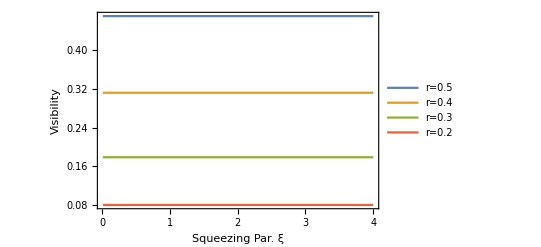

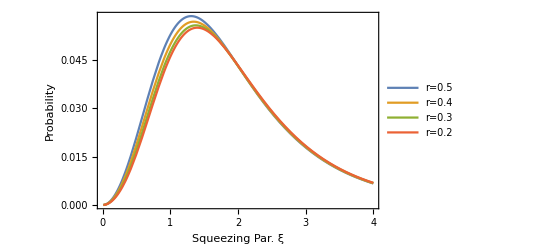

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.5,ξ],Vwo[0.4,ξ],Vwo[0.3,ξ],Vwo[0.2,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.4,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.2,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

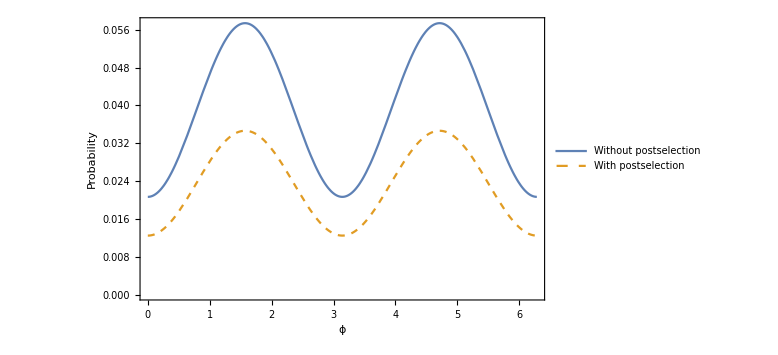

```mathematica
𝓇=0.5;
ξ=1.462;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0402491,{𝓇→0.999999,ξ→1.44364}}

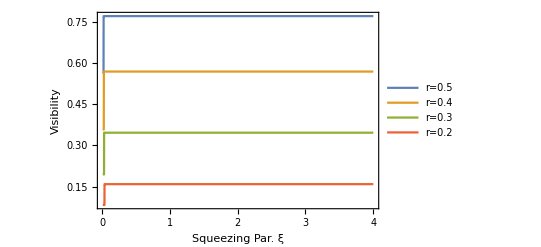

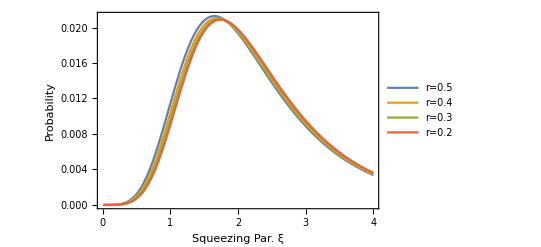

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.5,ξ],Vwo[0.4,ξ],Vwo[0.3,ξ],Vwo[0.2,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.4,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.2,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

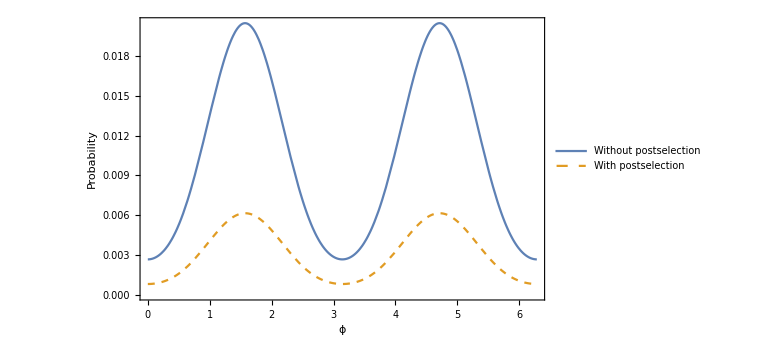

```mathematica
𝓇=0.5;
ξ=1.462;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/2)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/2 ca0 cb0)^k/k!,{k,0,n}];
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect2[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2
];
(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

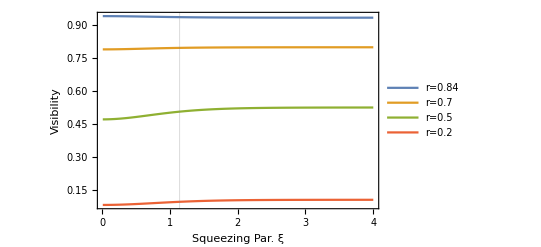

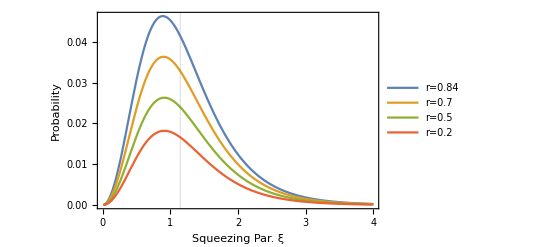

```mathematica
Plot[{Vwo2[0.84,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.2,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {1.144505936611957},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.84","r=0.7","r=0.5","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.84,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.2,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.84","r=0.7","r=0.5","r=0.2"},LabelStyle->Large,GridLines-> {{1.144505936611957},{}},ImageSize->Scaled[0.30]]
```

{0.0167249,{𝓇→0.00760683,ξ→0.906945}}

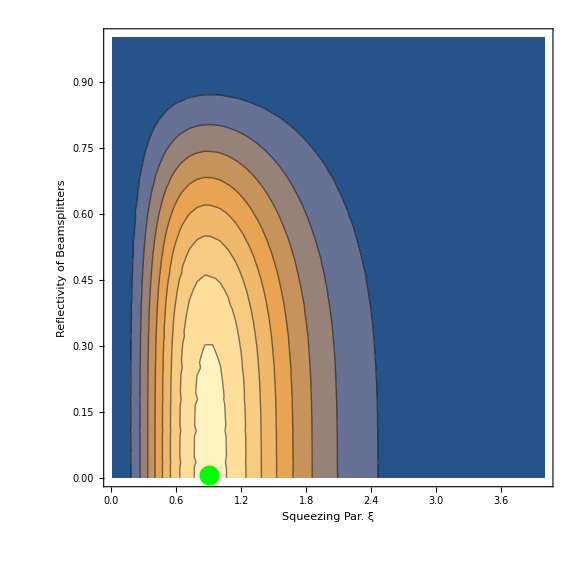

```mathematica
ClearAll[𝓇,ξ]
{val,sub}=FindMaximum[{wopostselect2[0,𝓇,ξ](1-Vwo2[𝓇,ξ]),0≤ 𝓇≤1&&0.01≤ξ≤ 4},{𝓇,0.8},{ξ,1}]
ContourPlot[wopostselect2[0,𝓇,ξ](1-Vwo2[𝓇,ξ]),{ξ,0.01,4},{𝓇,0,1},FrameLabel-> {"Squeezing Par. ξ","Reflectivity of Beamsplitters","Probability ×(1-Visibility)"},Frame-> True,PlotRange->Full,Epilog->{PointSize[0.025],Green,Point[{ξ/.sub,𝓇/.sub}]},ImageSize->Large,LabelStyle->Large]
```

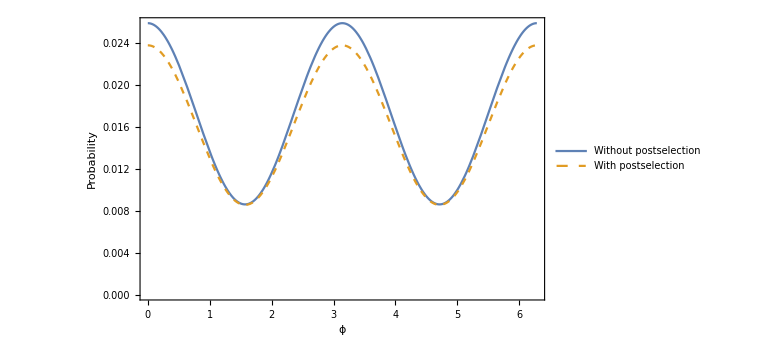

```mathematica
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 4. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/2)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out4,n]
n=5;
out4[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/2 ca0 cb0)^k/k!,{k,0,n}];
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
(*ψp=CoefficientList[out4[ca,cb],{cc3,cd3}];*)
ψp=CoefficientList[out4[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Total[Total[Table[Abs[√((i-1)!(j-1)!)ψ[[k,l]][[i,j]]]^2,{i,1,Dimensions[ψ[[k,l]]][[1]]},{j,1,Dimensions[ψ[[k,l]]][[1]]}]]],{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[Total[P]]
];
wopscoin[0,0.75,1]
```

Part::partw: Part 2 of {Sech[ξ]} does not exist.

Part::partw: Part 3 of {Sech[ξ]} does not exist.

Part::partw: Part 4 of {Sech[ξ]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {0} does not exist.

Part::partw: Part 3 of {0} does not exist.

Part::partw: Part 4 of {0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

0.491197+5719+13168189440000 Abs[{{Sech[1]},{0},{-0.0539825},{0},{0.00224835},{0},{-0.0000624288},{0},{1.30007×10^-6},{0},{-2.1659×10^-8}}⟦11,11⟧]^2
 |  |  |  |

```mathematica
(*-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]]*)
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[out4[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Abs[√(a!b!)ψ[[k,l]][[a+1,b+1]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Plot[{Vwocoin[0.84,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.2,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{1.14562},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.84","r=0.7","r=0.5","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.84,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.2,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.84","r=0.7","r=0.5","r=0.2"},GridLines->{{1.14562},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

Part::partw: Part 2 of {Sech[ξ]} does not exist.

Part::partw: Part 3 of {Sech[ξ]} does not exist.

Part::partw: Part 4 of {Sech[ξ]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {0} does not exist.

Part::partw: Part 3 of {0} does not exist.

Part::partw: Part 4 of {0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

Part::partw: Part 2 of {0} does not exist.

Part::partw: Part 3 of {0} does not exist.

Part::partw: Part 4 of {0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
wopscoin[0,0.5,1]
```

0.491197

{0.00582741,{𝓇→0.999833,ξ→1.19522}}

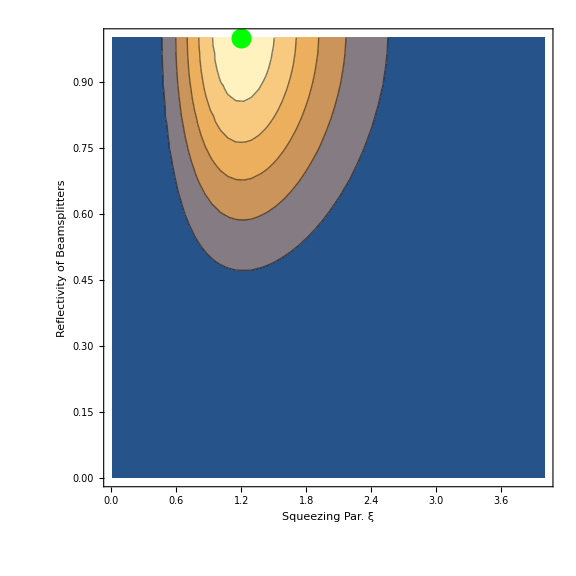

```mathematica
ClearAll[𝓇,ξ]
{val,sub}=FindMaximum[{wopscoin[0,𝓇,ξ](1-Vwocoin[𝓇,ξ]),0≤ 𝓇≤1&&0.01≤ξ≤ 4},{𝓇,0.8},{ξ,1}]
ContourPlot[wopscoin[0,𝓇,ξ](1-Vwocoin[𝓇,ξ]),{ξ,0.01,4},{𝓇,0,1},FrameLabel-> {"Squeezing Par. ξ","Reflectivity of Beamsplitters","Probability ×(1-Visibility)"},Frame-> True,PlotRange->Full,Epilog->{PointSize[0.025],Green,Point[{ξ/.sub,𝓇/.sub}]},ImageSize->Large,LabelStyle->Large]
```

```mathematica
wopscoin[0,𝓇,ξ]/.sub
```

0.0643324

```mathematica
Vwocoin[𝓇,ξ]/.sub
```

0.909417

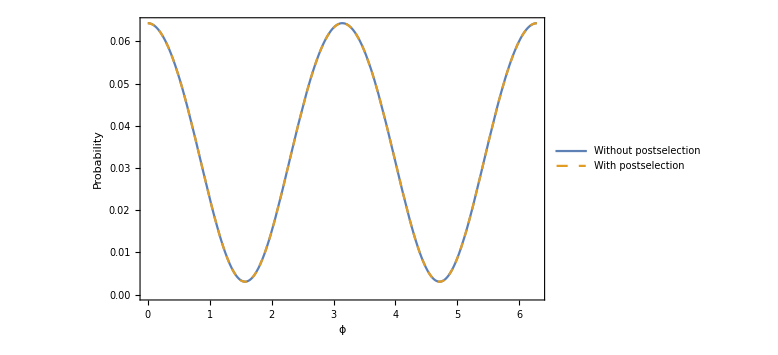

```mathematica
𝓇=𝓇/.sub;
ξ=ξ/.sub;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
```

## Debugging

```mathematica
ClearAll[mat,a,b,c,d,e,f,g,h,i]
mat={{a,b,c},{d,e,f},{g,h,i}};
mat//MatrixForm
Total[Total[mat]]-Total[mat,{1}][[1]]-Total[mat,{2}][[1]]+mat[[1,1]]
```

(a | b | c
d | e | f
g | h | i)

e+f+h+i

```mathematica
ψp=CoefficientList[1+ca cb + ca^2 cb+cc3^2 cd3 ca^3 cb,{cc3,cd3,ca,cb}];
ψp//MatrixForm
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}]
P=Table[Abs[√(a!b!)ψ[[k,l]][[a+1,b+1]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}]
Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]]
```

```mathematica
ψp//MatrixForm
ψp[[1,1]]//MatrixForm
```

((1 | 0
0 | 1
0 | 1
0 | 0) | (0 | 0
0 | 0
0 | 0
0 | 0)
(0 | 0
0 | 0
0 | 0
0 | 0) | (0 | 0
0 | 0
0 | 0
0 | 0)
(0 | 0
0 | 0
0 | 0
0 | 0) | (0 | 0
0 | 0
0 | 0
0 | 1))

(1 | 0
0 | 1
0 | 1
0 | 0)

```mathematica
ψ//MatrixForm
```

((1 | 0
0 | 1
0 | 1
0 | 0) | (0 | 0
0 | 0
0 | 0
0 | 0)
(0 | 0
0 | 0
0 | 0
0 | 0) | (0 | 0
0 | 0
0 | 0
0 | 0)
(0 | 0
0 | 0
0 | 0
0 | 0) | (0 | 0
0 | 0
0 | 0
0 | √2))

```mathematica
{a,b}
```

{0,0}

```mathematica
P//MatrixForm
```

(1 | 0
0 | 0
0 | 0)

```mathematica
Dimensions[ψp][[3]]
```

4

### Debugging

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=2;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselectdebug[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
coefftable
];
```

```mathematica
ClearAll[mat,a,b,c,d,e,f,g,h,i]
mat={{a,b,c},{d,e,f},{g,h,i}};
mat//MatrixForm
Table[Abs[√((k-1)!   (j-1)!)mat[[k,j]]]^1,{k,1,Dimensions[mat][[1]]},{j,1,Dimensions[mat][[2]]}]//MatrixForm
```

(a | b | c
d | e | f
g | h | i)

(Abs[a] | Abs[b] | √2 Abs[c]
Abs[d] | Abs[e] | √2 Abs[f]
√2 Abs[g] | √2 Abs[h] | 2 Abs[i])

```mathematica
CoefficientList[out[ca,cb,2],{cc3,cd3}]//MatrixForm
```

(0.74464-0.0000518924 ca^2+1.80813×10^-9 ca^4+0.000103785 ca cb ⅇ^(-ⅈ ϕ)-7.23253×10^-9 ca^3 cb ⅇ^(-ⅈ ϕ)-0.0000518924 cb^2 ⅇ^(-2 ⅈ ϕ)+1.08488×10^-8 ca^2 cb^2 ⅇ^(-2 ⅈ ϕ)-7.23253×10^-9 ca cb^3 ⅇ^(-3 ⅈ ϕ)+1.80813×10^-9 cb^4 ⅇ^(-4 ⅈ ϕ) | -0.00400912 ca+2.79387×10^-7 ca^3-0.00400912 ca ⅇ^(-ⅈ ϕ)+2.79387×10^-7 ca^3 ⅇ^(-ⅈ ϕ)+0.00400912 cb ⅇ^(-ⅈ ϕ)-8.3816×10^-7 ca^2 cb ⅇ^(-ⅈ ϕ)+0.00400912 cb ⅇ^(-2 ⅈ ϕ)-8.3816×10^-7 ca^2 cb ⅇ^(-2 ⅈ ϕ)+8.3816×10^-7 ca cb^2 ⅇ^(-2 ⅈ ϕ)+8.3816×10^-7 ca cb^2 ⅇ^(-3 ⅈ ϕ)-2.79387×10^-7 cb^3 ⅇ^(-3 ⅈ ϕ)-2.79387×10^-7 cb^3 ⅇ^(-4 ⅈ ϕ) | -0.0774344+0.0000161887 ca^2-0.154869 ⅇ^(-ⅈ ϕ)+0.0000323774 ca^2 ⅇ^(-ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-ⅈ ϕ)-0.0774344 ⅇ^(-2 ⅈ ϕ)+0.0000161887 ca^2 ⅇ^(-2 ⅈ ϕ)-0.0000647548 ca cb ⅇ^(-2 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-2 ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-3 ⅈ ϕ)+0.0000323774 cb^2 ⅇ^(-3 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-4 ⅈ ϕ) | 0.000416904 ca+0.00125071 ca ⅇ^(-ⅈ ϕ)-0.000416904 cb ⅇ^(-ⅈ ϕ)+0.00125071 ca ⅇ^(-2 ⅈ ϕ)-0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.000416904 ca ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.000416904 cb ⅇ^(-4 ⅈ ϕ) | 0.00402616+0.0161047 ⅇ^(-ⅈ ϕ)+0.024157 ⅇ^(-2 ⅈ ϕ)+0.0161047 ⅇ^(-3 ⅈ ϕ)+0.00402616 ⅇ^(-4 ⅈ ϕ)
0.00400912 ca-2.79387×10^-7 ca^3-0.00400912 ca ⅇ^(-ⅈ ϕ)+2.79387×10^-7 ca^3 ⅇ^(-ⅈ ϕ)-0.00400912 cb ⅇ^(-ⅈ ϕ)+8.3816×10^-7 ca^2 cb ⅇ^(-ⅈ ϕ)+0.00400912 cb ⅇ^(-2 ⅈ ϕ)-8.3816×10^-7 ca^2 cb ⅇ^(-2 ⅈ ϕ)-8.3816×10^-7 ca cb^2 ⅇ^(-2 ⅈ ϕ)+8.3816×10^-7 ca cb^2 ⅇ^(-3 ⅈ ϕ)+2.79387×10^-7 cb^3 ⅇ^(-3 ⅈ ϕ)-2.79387×10^-7 cb^3 ⅇ^(-4 ⅈ ϕ) | 0.154869-0.0000323774 ca^2-6.98896×10^-21 ca^2 ⅇ^(-ⅈ ϕ)+0.0000647548 ca cb ⅇ^(-ⅈ ϕ)-0.154869 ⅇ^(-2 ⅈ ϕ)+0.0000323774 ca^2 ⅇ^(-2 ⅈ ϕ)-0.0000323774 cb^2 ⅇ^(-2 ⅈ ϕ)-0.0000647548 ca cb ⅇ^(-3 ⅈ ϕ)+6.98896×10^-21 cb^2 ⅇ^(-3 ⅈ ϕ)+0.0000323774 cb^2 ⅇ^(-4 ⅈ ϕ) | -0.00125071 ca-0.00125071 ca ⅇ^(-ⅈ ϕ)+0.00125071 cb ⅇ^(-ⅈ ϕ)+0.00125071 ca ⅇ^(-2 ⅈ ϕ)+0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.00125071 ca ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-4 ⅈ ϕ) | -0.0161047-0.0322093 ⅇ^(-ⅈ ϕ)+0.0322093 ⅇ^(-3 ⅈ ϕ)+0.0161047 ⅇ^(-4 ⅈ ϕ) | 0
-0.0774344+0.0000161887 ca^2+0.154869 ⅇ^(-ⅈ ϕ)-0.0000323774 ca^2 ⅇ^(-ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-ⅈ ϕ)-0.0774344 ⅇ^(-2 ⅈ ϕ)+0.0000161887 ca^2 ⅇ^(-2 ⅈ ϕ)+0.0000647548 ca cb ⅇ^(-2 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-2 ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-3 ⅈ ϕ)-0.0000323774 cb^2 ⅇ^(-3 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-4 ⅈ ϕ) | 0.00125071 ca-0.00125071 ca ⅇ^(-ⅈ ϕ)-0.00125071 cb ⅇ^(-ⅈ ϕ)-0.00125071 ca ⅇ^(-2 ⅈ ϕ)+0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.00125071 ca ⅇ^(-3 ⅈ ϕ)+0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-4 ⅈ ϕ) | 0.024157-7.1567×10^-18 ⅇ^(-ⅈ ϕ)-0.048314 ⅇ^(-2 ⅈ ϕ)-7.1567×10^-18 ⅇ^(-3 ⅈ ϕ)+0.024157 ⅇ^(-4 ⅈ ϕ) | 0 | 0
-0.000416904 ca+0.00125071 ca ⅇ^(-ⅈ ϕ)+0.000416904 cb ⅇ^(-ⅈ ϕ)-0.00125071 ca ⅇ^(-2 ⅈ ϕ)-0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.000416904 ca ⅇ^(-3 ⅈ ϕ)+0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.000416904 cb ⅇ^(-4 ⅈ ϕ) | -0.0161047+0.0322093 ⅇ^(-ⅈ ϕ)-0.0322093 ⅇ^(-3 ⅈ ϕ)+0.0161047 ⅇ^(-4 ⅈ ϕ) | 0 | 0 | 0
0.00402616-0.0161047 ⅇ^(-ⅈ ϕ)+0.024157 ⅇ^(-2 ⅈ ϕ)-0.0161047 ⅇ^(-3 ⅈ ϕ)+0.00402616 ⅇ^(-4 ⅈ ϕ) | 0 | 0 | 0 | 0)

```mathematica
1/(√(c!d!))CoefficientList[CoefficientList[out[ca,cb,2],{cc3,cd3}][[1+1,1+1]],{ca,cb}]//MatrixForm
```

((0.154869-0.154869 ⅇ^(-2 ⅈ ϕ))/(√(c! d!)) | 0 | (-0.0000323774 ⅇ^(-2 ⅈ ϕ)+6.98896×10^-21 ⅇ^(-3 ⅈ ϕ)+0.0000323774 ⅇ^(-4 ⅈ ϕ))/(√(c! d!))
0 | (0.0000647548 ⅇ^(-ⅈ ϕ)-0.0000647548 ⅇ^(-3 ⅈ ϕ))/(√(c! d!)) | 0
(-0.0000323774-6.98896×10^-21 ⅇ^(-ⅈ ϕ)+0.0000323774 ⅇ^(-2 ⅈ ϕ))/(√(c! d!)) | 0 | 0)

```mathematica
1/(√(c!d!))CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}]
```

Part::pkspec1: The expression 1+c cannot be used as a part specification.

{{1/(√(c! d!)){{0.74464-0.0000518924 ca^2+1.80813×10^-9 ca^4+0.000103785 ca cb ⅇ^(-ⅈ ϕ)-7.23253×10^-9 ca^3 cb ⅇ^(-ⅈ ϕ)-0.0000518924 cb^2 ⅇ^(-2 ⅈ ϕ)+1.08488×10^-8 ca^2 cb^2 ⅇ^(-2 ⅈ ϕ)-7.23253×10^-9 ca cb^3 ⅇ^(-3 ⅈ ϕ)+1.80813×10^-9 cb^4 ⅇ^(-4 ⅈ ϕ),-0.00400912 ca+2.79387×10^-7 ca^3-0.00400912 ca ⅇ^(-ⅈ ϕ)+2.79387×10^-7 ca^3 ⅇ^(-ⅈ ϕ)+0.00400912 cb ⅇ^(-ⅈ ϕ)-8.3816×10^-7 ca^2 cb ⅇ^(-ⅈ ϕ)+0.00400912 cb ⅇ^(-2 ⅈ ϕ)-8.3816×10^-7 ca^2 cb ⅇ^(-2 ⅈ ϕ)+8.3816×10^-7 ca cb^2 ⅇ^(-2 ⅈ ϕ)+8.3816×10^-7 ca cb^2 ⅇ^(-3 ⅈ ϕ)-2.79387×10^-7 cb^3 ⅇ^(-3 ⅈ ϕ)-2.79387×10^-7 cb^3 ⅇ^(-4 ⅈ ϕ),-0.0774344+0.0000161887 ca^2-0.154869 ⅇ^(-ⅈ ϕ)+0.0000323774 ca^2 ⅇ^(-ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-ⅈ ϕ)-0.0774344 ⅇ^(-2 ⅈ ϕ)+0.0000161887 ca^2 ⅇ^(-2 ⅈ ϕ)-0.0000647548 ca cb ⅇ^(-2 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-2 ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-3 ⅈ ϕ)+0.0000323774 cb^2 ⅇ^(-3 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-4 ⅈ ϕ),0.000416904 ca+0.00125071 ca ⅇ^(-ⅈ ϕ)-0.000416904 cb ⅇ^(-ⅈ ϕ)+0.00125071 ca ⅇ^(-2 ⅈ ϕ)-0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.000416904 ca ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.000416904 cb ⅇ^(-4 ⅈ ϕ),0.00402616+0.0161047 ⅇ^(-ⅈ ϕ)+0.024157 ⅇ^(-2 ⅈ ϕ)+0.0161047 ⅇ^(-3 ⅈ ϕ)+0.00402616 ⅇ^(-4 ⅈ ϕ)},{0.00400912 ca-2.79387×10^-7 ca^3-0.00400912 ca ⅇ^(-ⅈ ϕ)+2.79387×10^-7 ca^3 ⅇ^(-ⅈ ϕ)-0.00400912 cb ⅇ^(-ⅈ ϕ)+8.3816×10^-7 ca^2 cb ⅇ^(-ⅈ ϕ)+0.00400912 cb ⅇ^(-2 ⅈ ϕ)-8.3816×10^-7 ca^2 cb ⅇ^(-2 ⅈ ϕ)-8.3816×10^-7 ca cb^2 ⅇ^(-2 ⅈ ϕ)+8.3816×10^-7 ca cb^2 ⅇ^(-3 ⅈ ϕ)+2.79387×10^-7 cb^3 ⅇ^(-3 ⅈ ϕ)-2.79387×10^-7 cb^3 ⅇ^(-4 ⅈ ϕ),0.154869-0.0000323774 ca^2-6.98896×10^-21 ca^2 ⅇ^(-ⅈ ϕ)+0.0000647548 ca cb ⅇ^(-ⅈ ϕ)-0.154869 ⅇ^(-2 ⅈ ϕ)+0.0000323774 ca^2 ⅇ^(-2 ⅈ ϕ)-0.0000323774 cb^2 ⅇ^(-2 ⅈ ϕ)-0.0000647548 ca cb ⅇ^(-3 ⅈ ϕ)+6.98896×10^-21 cb^2 ⅇ^(-3 ⅈ ϕ)+0.0000323774 cb^2 ⅇ^(-4 ⅈ ϕ),-0.00125071 ca-0.00125071 ca ⅇ^(-ⅈ ϕ)+0.00125071 cb ⅇ^(-ⅈ ϕ)+0.00125071 ca ⅇ^(-2 ⅈ ϕ)+0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.00125071 ca ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-4 ⅈ ϕ),-0.0161047-0.0322093 ⅇ^(-ⅈ ϕ)+0.0322093 ⅇ^(-3 ⅈ ϕ)+0.0161047 ⅇ^(-4 ⅈ ϕ),0},{-0.0774344+0.0000161887 ca^2+0.154869 ⅇ^(-ⅈ ϕ)-0.0000323774 ca^2 ⅇ^(-ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-ⅈ ϕ)-0.0774344 ⅇ^(-2 ⅈ ϕ)+0.0000161887 ca^2 ⅇ^(-2 ⅈ ϕ)+0.0000647548 ca cb ⅇ^(-2 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-2 ⅈ ϕ)-0.0000323774 ca cb ⅇ^(-3 ⅈ ϕ)-0.0000323774 cb^2 ⅇ^(-3 ⅈ ϕ)+0.0000161887 cb^2 ⅇ^(-4 ⅈ ϕ),0.00125071 ca-0.00125071 ca ⅇ^(-ⅈ ϕ)-0.00125071 cb ⅇ^(-ⅈ ϕ)-0.00125071 ca ⅇ^(-2 ⅈ ϕ)+0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.00125071 ca ⅇ^(-3 ⅈ ϕ)+0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.00125071 cb ⅇ^(-4 ⅈ ϕ),0.024157-7.1567×10^-18 ⅇ^(-ⅈ ϕ)-0.048314 ⅇ^(-2 ⅈ ϕ)-7.1567×10^-18 ⅇ^(-3 ⅈ ϕ)+0.024157 ⅇ^(-4 ⅈ ϕ),0,0},{-0.000416904 ca+0.00125071 ca ⅇ^(-ⅈ ϕ)+0.000416904 cb ⅇ^(-ⅈ ϕ)-0.00125071 ca ⅇ^(-2 ⅈ ϕ)-0.00125071 cb ⅇ^(-2 ⅈ ϕ)+0.000416904 ca ⅇ^(-3 ⅈ ϕ)+0.00125071 cb ⅇ^(-3 ⅈ ϕ)-0.000416904 cb ⅇ^(-4 ⅈ ϕ),-0.0161047+0.0322093 ⅇ^(-ⅈ ϕ)-0.0322093 ⅇ^(-3 ⅈ ϕ)+0.0161047 ⅇ^(-4 ⅈ ϕ),0,0,0},{0.00402616-0.0161047 ⅇ^(-ⅈ ϕ)+0.024157 ⅇ^(-2 ⅈ ϕ)-0.0161047 ⅇ^(-3 ⅈ ϕ)+0.00402616 ⅇ^(-4 ⅈ ϕ),0,0,0,0}}⟦1+c,1+d⟧}}